# Question 1:

```mathematica
ClearAll["Global`*"]
(* Defining Prefix Constants *)
engH=-e^2/(8 π eps0 a0);
```

```mathematica
(* Defining Helping Functions *)
Delta[x_]:=Exp[-x] (1+x+x^2/3);
Deltap[x_]:=Exp[x] (1-x+x^2/3);
Jay[x_]:=-2 engH(-x^-1 + Exp[-2x] (1+x^-1));
Kay[x_]:=2 engH Exp[-x] (1+x);
Jayp[x_]:=-2 engH(x^-1-Exp[-2x](x^-1+11/8+3x/4+x^2/6));
Kayp[x_]:=-2 engH/5(-Exp[-2x] (-25/8+23x/4+3 x^2+x^3/3)+6/x (
Delta[x]^2 (EulerGamma+Log[x])+Deltap[x]^2 ExpIntegralEi[-4x]-
2 Delta[x] Deltap[x] ExpIntegralEi[-2x]));
```

```mathematica
(* Defining Energy Functions *)
SymEng[x_]:=2 engH-2 engH x^-1+(1+Delta[x]^2)^-1 ×
(2Jay[x]+Jayp[x]+2Delta[x]Kay[x]+Kayp[x]);
AntEng[x_]:=2 engH-2 engH x^-1+(1-Delta[x]^2)^-1 ×
(2Jay[x]+Jayp[x]-2Delta[x]Kay[x]-Kayp[x]);
```

## A. Plot energies functions vs bond distance

```mathematica
(* Temporary set parameters for plotting *) 
a0:=1; e:=1; eps0:=1;
```

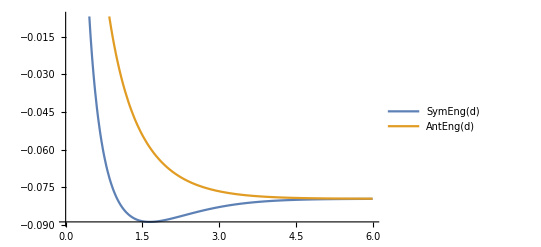

```mathematica
Plot[{SymEng[d],AntEng[d]},{d,0,6},PlotLegends->"Expressions"]
```

## B. “Classical” bonding energy plotting

```mathematica
(* Defining function to the classical energy *)
ClsEng[x_]:=2 engH-2engH x^-1+2Jay[x]+Jayp[x];
```

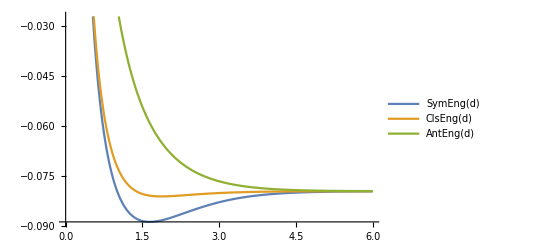

```mathematica
Plot[{SymEng[d],ClsEng[d],AntEng[d]},{d,0,6},PlotLegends->"Expressions"]
```

```mathematica
(* Postprocess: cleaning temporary parameters *)
Clear[a0, e, eps0];
```

## C. Find equilibrium bond length for E_s and E_n

## D. Find minimum energy for E_s and E_n

They all can be solved together by a single function.

```mathematica
(* Setting Real World Constants *)
a0=Quantity[1, "BohrRadius"];
eps0 =Quantity[1, "ElectricConstant"];
e=Quantity[1, "ElementaryCharge"];
```

```mathematica
FindMinimum[SymEng[d], {d,0.1,6}]
```

{-4.86512×10^-18 kg m^2/s^2,{d→1.66205}}

```mathematica
FindMinimum[ClsEng[d], {d,0.1,6}]
```

{-4.44466×10^-18 kg m^2/s^2,{d→1.93382}}

## E. Curve Fitting near eq. bond length for E_s and E

```mathematica
(*
 * Helper function for numerial analysis.
* Mathematica does not perform fitting with
* untis well, thus we only use numerical
* fitting in this section.
 *)
fitUnitNum=50;
JSpec:=QuantityMagnitude[UnitConvert[#,"Joules"]]&;
```

FittedModel[-4.86764×10^-18+7.21724×10^-19 (-1.6653+x)^2]

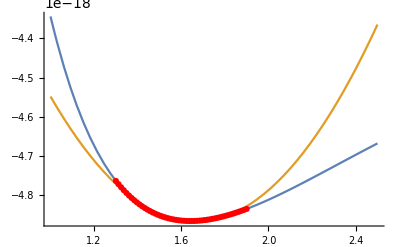

```mathematica
(* Caching sample data and fitting on Subscript[E, s] *)
symFitD=Table[{d,JSpec@SymEng[d]},{d,1.3,1.9,0.6/fitUnitNum}];
symFit=NonlinearModelFit[symFitD, E0+2^-1 k (x-x0)^2,{E0,k,{x0,1.6}},x]

(* Check curve fitting result *)
plot1=Plot[{JSpec@SymEng[d],symFit[d]},{d,1,2.5}];
plot2=ListPlot[symFitD, PlotStyle->Red];
Show[plot1, plot2,PlotRange-> All,AxesOrigin-> Automatic]
```

```mathematica
symFit["BestFitParameters"]
```

{E0→-4.86764×10^-18,k→1.44345×10^-18,x0→1.6653}

```mathematica
(* Assign related parameters *)
symFitK=Quantity[1.44*^-18,"Joules"]×a0^-2//UnitConvert
symFitX0=1.67 a0//UnitConvert
```

514.233 kg/s^2

8.83726×10^-11 m

k =

514.233 kg/s^2

x_0 =

8.83726×10^-11 m

FittedModel[-4.44527×10^-18+1.65379×10^-19 (-1.91082+x)^2]

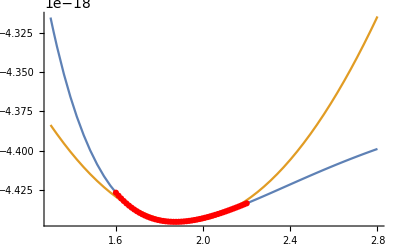

```mathematica
(* Caching sample data and fitting on Subscript[E, s] *)
clsFitD=Table[{d,JSpec@ClsEng[d]},{d,1.6,2.2,0.6/fitUnitNum}];
clsFit=NonlinearModelFit[clsFitD, E0+2^-1 k (x-x0)^2,{E0,k,{x0,1.9}},x]

(* Check curve fitting result *)
plot1=Plot[{JSpec@ClsEng[d],clsFit[d]},{d,1.3,2.8}];
plot2=ListPlot[clsFitD, PlotStyle->Red];
Show[plot1, plot2,PlotRange-> All,AxesOrigin-> Automatic]
```

```mathematica
clsFit["BestFitParameters"]
```

{E0→-4.44527×10^-18,k→3.30759×10^-19,x0→1.91082}

```mathematica
(* Assign related parameters *)
clsFitK=Quantity[3.31*^-19,"Joules"]×(a0)^-2//UnitConvert
clsFitX0=1.91 a0//UnitConvert
```

118.202 kg/s^2

1.01073×10^-10 m

k =

118.202 kg/s^2

x_0 =

1.01073×10^-10 m

## F. Calculate Frequencies

```mathematica
(* Defining frequency function *)
c:=Quantity[1,"SpeedOfLight"];
avo:=Quantity[1,"AvogadroNumber"];
mu:=Quantity[1/2,"Grams"] avo^-1//UnitConvert;
FreqW[k_]:=(2π c)^-1 Sqrt[k/mu]//UnitConvert[#,1/"Centimeters"]&;
```

```mathematica
(* For Subscript[E, s] fitting model *)
symV=FreqW[symFitK]
```

4178.02 /cm

```mathematica
(* For Subscript[E, n] fitting model *)
clsV=FreqW[clsFitK]
```

2003.1 /cm

```mathematica
RelErr[x_, xTruth_]:=Abs[x-xTruth]/xTruth;
expV=Quantity[4417,1/"Centimeters"];
```

```mathematica
(* Error from Subscript[E, s] to experiment result *)
symV~RelErr~expV
```

0.0541057

```mathematica
(* Error from Subscript[E, s] to experiment result *)
clsV~RelErr~expV
```

0.546502